```mathematica
F[x1_,x2_]=x1^4+x2^4-2 x1^2 -4x1 x2-2 x2^2 ; (* задана функція *)
X={{1.,-1.}}; (*початкове наближення*)
ϵ=10^-3; (*задана точність*)
```

```mathematica
(*значення мінімума, знайдене за допомогою вбудованої функції*)
```

```mathematica
MinF=FindMinimum[F[x1,x2],{{x1,X[[-1,1]]},{x2,X[[-1,2]]}}][[2,1;;2,2]]
```

{1.41421,1.41421}

```mathematica
(*графік тривимірної реалізації*)
Show[Plot3D[F[x,y],{x,-4,4},{y,-4,4}]]
```

-Graphics3D-

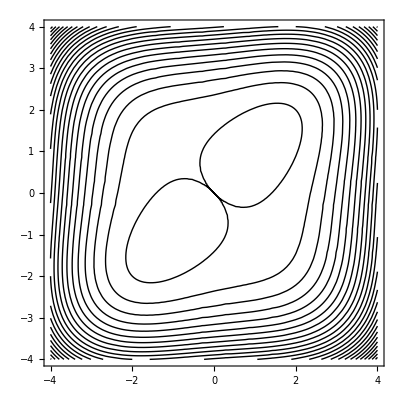

```mathematica
(*двовимірний графік ліній рівня*) 
CP=ContourPlot[F[x,y],{x,-4,4},{y,-4,4},Contours->{Automatic,50},ContourShading->None,AspectRatio->Automatic]
```

```mathematica
(* метод найшвидшого спуску *)
```

```mathematica
t30=AbsoluteTime[]; (*початок відліку часу*)
X3=X;
Clear[α]
Α={};
i=1;
res3={};
While[Norm[Grad[F[x1,x2],{x1,x2}]/.{x1->X3[[-1,1]],x2->X3[[-1,2]]}]>ϵ,{
If[Length[X3]≥100,Break[]];
Clear[α];
a=0.;
b=.2;
AB={};
AppendTo[AB,{a,b}];

(* одновимірна мінімізація *)
(*temp - вектор*)
temp=X3[[-1]]-α  (Grad[F[x1,x2],{x1,x2}]/.{x1->X3[[-1,1]],x2->X3[[-1,2]]});
FF[α_]=F[temp[[1]],temp[[2]]];

(*метод дихотомії*)
For[k = 0, k < 1000, k++ ,
{x0=(AB[[-1,1]]+AB[[-1,2]])/2;
Fx0=FF[x0];
x1k=x0-ϵ/2; 
x2k=x0+ϵ/2;
 Fx={FF[x1k], FF[x2k]};
If[Fx[[1]]< Fx[[2]], {
a=a; 
b=x0;
 AppendTo[AB,{a,b}]
}, {
a=x0;
 b=b;
 AppendTo[AB,{a,b}]
}];
If[Abs[AB[[-1,2]]-AB[[-1,1]]]≤  ϵ, {
α=(a+b)/2;
AppendTo[Α,α];
Break[];
}];
}];
(*метод дихотомії для мінімізації функції можна замінити вбудованою функцією*)
(*α=NMinimize[FF[α],a<α<b,α][[2,1,2]];
AppendTo[Α,α];*)
AppendTo[X3,X3[[-1]]-α*Grad[F[x1,x2],{x1,x2}]/.{x1->X3[[-1,1]],x2->X3[[-1,2]]}];
AppendTo[res3,{i++,X3[[-1]],F[X3[[-1,1]],X3[[-1,2]]],α}];
}]
t31=AbsoluteTime[];
Grid[Prepend[res3,{"k","x^*","F(x^*)","α_k"}]]
Print["Час роботи методу: ",t3=t31-t30,"\nТочне наближення: ", X3[[-1]],"\nЗначеня функції в отриманому значенні: ", F[X3[[-1,1]],X3[[-1,2]]]]
```

k | x^* | F(x^*) | α_k
1 | {0.201562,-0.201562} | 0.00330118 | 0.199609
2 | {0.195024,-0.195024} | 0.00289323 | 0.199609
3 | {0.189102,-0.189102} | 0.00255747 | 0.199609
4 | {0.183702,-0.183702} | 0.00227766 | 0.199609
5 | {0.178753,-0.178753} | 0.00204193 | 0.199609
6 | {0.174192,-0.174192} | 0.00184139 | 0.199609
7 | {0.169972,-0.169972} | 0.00166933 | 0.199609
8 | {0.166051,-0.166051} | 0.00152055 | 0.199609
9 | {0.162396,-0.162396} | 0.001391 | 0.199609
10 | {0.158976,-0.158976} | 0.00127749 | 0.199609
11 | {0.155768,-0.155768} | 0.00117746 | 0.199609
12 | {0.15275,-0.15275} | 0.00108883 | 0.199609
13 | {0.149905,-0.149905} | 0.00100993 | 0.199609
14 | {0.147215,-0.147215} | 0.000939377 | 0.199609
15 | {0.144668,-0.144668} | 0.000876026 | 0.199609
16 | {0.14225,-0.14225} | 0.000818923 | 0.199609
17 | {0.139952,-0.139952} | 0.000767268 | 0.199609
18 | {0.137763,-0.137763} | 0.000720386 | 0.199609
19 | {0.135676,-0.135676} | 0.000677703 | 0.199609
20 | {0.133682,-0.133682} | 0.000638731 | 0.199609
21 | {0.131774,-0.131774} | 0.000603048 | 0.199609
22 | {0.129947,-0.129947} | 0.000570294 | 0.199609
23 | {0.128195,-0.128195} | 0.000540154 | 0.199609
24 | {0.126513,-0.126513} | 0.000512356 | 0.199609
25 | {0.124896,-0.124896} | 0.000486664 | 0.199609
26 | {0.123341,-0.123341} | 0.000462867 | 0.199609
27 | {0.121843,-0.121843} | 0.000440785 | 0.199609
28 | {0.120398,-0.120398} | 0.000420254 | 0.199609
29 | {0.119005,-0.119005} | 0.000401134 | 0.199609
30 | {0.11766,-0.117659} | 0.000383296 | 0.199609
31 | {0.11636,-0.116357} | 0.000366628 | 0.199609
32 | {0.115105,-0.115097} | 0.000351029 | 0.199609
33 | {0.113894,-0.113873} | 0.00033641 | 0.199609
34 | {0.112731,-0.112677} | 0.000322686 | 0.199609
35 | {0.11163,-0.111492} | 0.000309761 | 0.199609
36 | {0.11063,-0.110275} | 0.000297419 | 0.199609
37 | {0.109833,-0.10892} | 0.000284602 | 0.199609
38 | {0.109503,-0.10716} | 0.000264669 | 0.199609
39 | {0.110326,-0.104307} | 0.000194074 | 0.199609
40 | {0.114059,-0.0985952} | -0.000214511 | 0.199609
41 | {0.125221,-0.0854831} | -0.00285893 | 0.199609
42 | {0.155382,-0.0532561} | -0.0202682 | 0.199609
43 | {0.233927,0.0284052} | -0.134641 | 0.199609
44 | {0.433162,0.237843} | -0.86209 | 0.199609
45 | {0.904025,0.762856} | -4.5504 | 0.199609
46 | {1.40431,1.4221} | -7.99809 | 0.134766
47 | {1.41384,1.41381} | -8. | 0.0417969
48 | {1.4142,1.41422} | -8. | 0.0621094

Час роботи методу: 0.039217
Точне наближення: {1.4142,1.41422}
Значеня функції в отриманому значенні: -8.

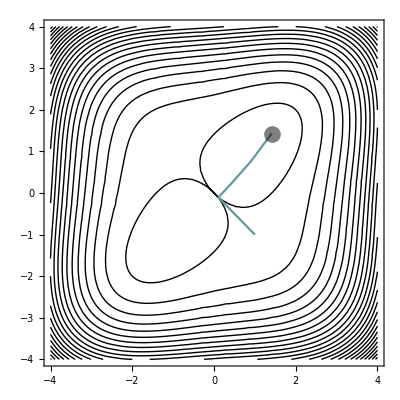

```mathematica
(*траєкторія пошука мінімума функції*)
Show[CP,ListLinePlot[X3,ColorFunction->"Rainbow",PlotRange->All],Graphics[{Opacity[0.5],Black,PointSize[0.03],Point[{point[[1]],point[[2]]}]}]]
```